This is Mathematica notebook for simulating long-term polymorphism reported in “Positive feedback between demographic and selective fluctuations can greatly amplify the random fluctuation of population size” by Yuseob Kim

```mathematica
Rep=1; (* number of replicates *)
Cap=2000; (* total population size = filed + refuge *)
senv =0.2; sran=0.1; (* senv = a_S, sran = b_S *)
fenv=0.3; fran=0.1; (* fenv = a_U, fran = b_U *)
renv=0.05; rran=0.1; (* renv = a_V, rran = b_V *)
dregul=10000; (* dregul is parameter g in Kim (2023); a large positive value sets soft selection. A negative value sets hard selection *)
Lseq=4; (* the number of loci *)
NSelSite=4;  (* the number of loci under selection; as this study does not include neutral loci, you need to set Lseq = NSelSite *)
selco=Table[{0,1},{l,1,NSelSite}];
selco=Join[selco,Table[{0,0},{l,1,Lseq-NSelSite}]];
rmut=0.00002; (* mutation rate per locus per generation *)
rmig12=0.5; (* probability for a haploid in the field to move to the refuge in the migration step *)
rmig21=0.5;(* probability for a haploid in the refuge to move to the field in the migration step *)
rrec=0.01; (* recombination rate between adjacent loci per generation *)
TotGen=30000; (* the length (generation) of a single simulation run *)
intvl=5000; 
For[rep=0,rep<Rep,rep++;
FFreqTraj={};
RFreqTraj={};
NPopTraj={};
PField={Cap/2};HField={0};
PRefuge={Cap/2};HRefuge={0}; (* simulation starts with Cap/2 individuals in the field and refuge each, with haplotype 0 [= 000...0] *)
mHetTraj={};
NScorr={};
gen=0;
AF=mHet=Table[0,{l,1,Lseq}];
mmHet=0;
m01=m15=m59=m910=0;
While[
gen<TotGen,
gen++;
{PField,HField}=Mutation[PField,HField, rmut Lseq,Lseq]; (* mutation step in the field *)
{PField,HField}=Recombination[PField,HField,rrec Lseq,Lseq]; (* recombination step in the field *)
{PRefuge,HRefuge}=Mutation[PRefuge,HRefuge, rmut Lseq,Lseq];
{PRefuge,HRefuge}=Recombination[PRefuge,HRefuge,rrec Lseq,Lseq];
env=RandomVariate[NormalDistribution[]]; (* sampling Z_1 *)

HFitL=HaploFit[HField, AMFfitRF[env,senv, sran, selco,Lseq],Lseq]; (* sampling fitness for all haplotypes with positive frequencies *)
HFitLR=Table[1,{i,1,Length[HRefuge]}]; (* relative fitness is 1 for all haplotypes in the refuge *)
Kf=0.5Cap Exp[fenv env+fran RandomVariate[NormalDistribution[]]]; (* sampling the carrying capacity of the field *)
{PField,HField}=PoissonReproduceRF[PField, HField,HFitL, Kf, dregul]; (* reproduction in the field *)
Kr= 0.5Cap Exp[renv env+rran RandomVariate[NormalDistribution[]]];(* sampling the carrying capacity of the refuge *)
{PRefuge,HRefuge}=PoissonReproduceRF[PRefuge, HRefuge,HFitLR, Kr, dregul]; (* reproduction in the refuge *)
NNF=Total[PField];NNR=Total[PRefuge];

{PField,HField, PRefuge,HRefuge}=Migration[PField,HField,PRefuge,HRefuge,rmig12,rmig21]; (* exchange of individuals between the field and refuge *)
NF=Total[PField];nHField=Length[PField];
NR=Total[PRefuge];nHRefuge=Length[PRefuge];
If[(NF==0)||(NR==0),Print[{gen,NF,NR}];Break[]];
FFreq=Table[Count1[PField, HField,nHField,site],{site,1,Lseq}]; (* counting individuals with '1' allele (= A2 allele) in the field *)
FFreqTraj=Append[FFreqTraj,FFreq];
RFreq=Table[Count1[PRefuge, HRefuge,nHRefuge,site],{site,1,Lseq}];
RFreqTraj=Append[RFreqTraj,RFreq];
NPopTraj=Append[NPopTraj,{NF,NR}];
For[site=0,site<Lseq,site++;
AF[[site]]=1.0(FFreq[[site]]+RFreq[[site]])/(NF+NR); (* allele frequency in the total population *)
mHet[[site]]+=2AF[[site]](1-AF[[site]]); (* site heterozygosity *)
If[AF[[site]]<0.1, m01++,
If[AF[[site]]<0.5,m15++,If[AF[[site]]<0.9,m59++, m910++]] (* putting an allele frequency into [0, 0.1), [0.1, 0.5), [0.5, 0.9) or [0.9, 1] bins *)
]
];
If[Mod[gen,intvl]==0,
Print[{gen, AF}]
]
];
FreqDist=Append[FreqDist,AF];
For[site=0, site<Lseq,site++;
mHet[[site]]/=TotGen;
mmHet +=mHet[[site]]/Lseq;
];
Print[mHet," het=",mmHet];
m01/=(Lseq TotGen);m15/=(Lseq TotGen); m59/=(Lseq TotGen);m910/=(Lseq TotGen);
Print["p[0,0.1]=",1.0 m01," p[0.1,0.5]=", 1.0 m15," p[0.5,0.9]=",1.0m59, " p[0.9,1]=",1.0m910]
];
TAllFix=gen;
vars=senv^2+sran^2;
covsf=senv fenv;
covsr=senv renv;
covfr=fenv renv;
If[vars>0,Phi =(covsf-covsr)/vars;Print["Phi=",Phi],Print["Neutral"]]
```

{5000,{0.000512558,0.,0.483854,0.307535}}

{10000,{0.,0.262522,0.573057,0.410017}}

{15000,{0.641746,1.,0.441746,0.13055}}

{20000,{0.,0.270748,0.,0.128595}}

{25000,{0.253465,0.183168,0.152475,0.360891}}

{30000,{0.,0.837683,0.,0.923278}}

{0.142195,0.144431,0.196308,0.242069} het=0.181251

p[0,0.1]=0.387975 p[0.1,0.5]=0.227892 p[0.5,0.9]=0.198742 p[0.9,1]=0.185392

Phi=1.

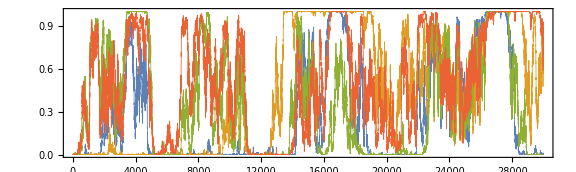

```mathematica
RelFreqList=Table[(FFreqTraj[[gen]][[site]]+RFreqTraj[[gen]][[site]])/Total[NPopTraj[[gen]]],{site,1,Lseq},{gen,1,TotGen}];
gFreq=ListPlot[RelFreqList,Joined->True,Frame->True, PlotStyle->Thickness[0.001],PlotRange->{0,1},AspectRatio->0.3, ImageSize->Large]
```